```mathematica
Clear[Nm]
```

```mathematica
X[J_,μ_]:= 1/2(J+μ);
B[J_]:= Exp[-J];
```

```mathematica
λp[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]+√((Sinh[X[J,μ]])^2+B[J]));
λm[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]-√((Sinh[X[J,μ]])^2+B[J]));
```

```mathematica
vm[J_,μ_]:= Exp[-μ/2](λm[J,μ]-1);
```

```mathematica
ϕav[J_,μ_,Nm_]:=(λp[J,μ]^Nm+λm[J,μ]^Nm vm[J,μ]^2)/((λp[J,μ]^Nm+λm[J,μ]^Nm)(1+vm[J,μ]^2));
```

```mathematica
ϕav2[J_,μ_,Nm_]:= (λp[J,μ]^Nm(1+vm[J,μ]^2)+λm[J,μ]^Nm(vm[J,μ]^2+vm[J,μ]^4))/((λp[J,μ]^Nm+λm[J,μ]^Nm)(1+vm[J,μ]^2)^2);
```

```mathematica
var[J_,μ_,Nm_]:= Abs[ϕav[J,μ,Nm]-ϕav[J,μ,Nm]^2]
```

```mathematica
var[2,-0.57,16]
```

0.0457314

```mathematica
ϕav2[1,-0.57,12]
```

0.668197

```mathematica
ϕav[2,-0.57,100]^2
```

0.906229

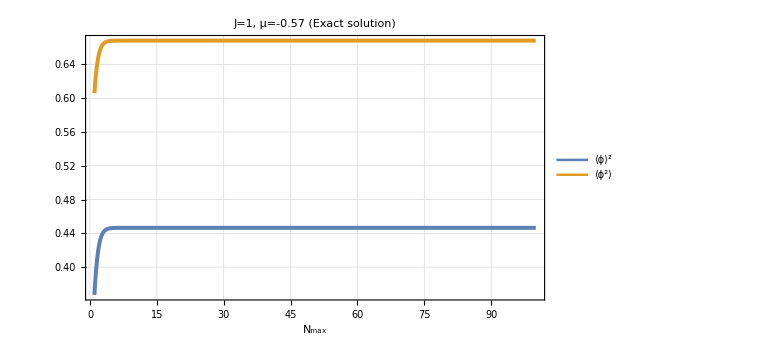

```mathematica
Plot[{ϕav[1,-0.57,Nm]^2,ϕav2[1,-0.57,Nm]},{Nm,1,100}, ImageSize->Large, PlotRange->Full, Frame->True, GridLines->Automatic, FrameLabel->{"N_max"}, LabelStyle->{GrayLevel[0],12},PlotStyle->{{Thickness[0.005]},{Thickness[0.005]}},PlotLegends->Placed[LineLegend[{"⟨ϕ⟩^2","⟨ϕ^2⟩"},LegendFunction->Frame],{{0.7,0.6},{0.65,0.6}}], PlotLabel->"J=1, μ=-0.57 (Exact solution)"]
```